```mathematica
SurfaceData["Cone", "ParametricEquations"]
```

Function[a,Function[{u,v},{a u Cos[v],a u Sin[v],u}]]

```mathematica
Function[a,Function[{u,v},{a u Cos[v],a u Sin[v],u}]][1][θ,ϕ]
```

{θ Cos[ϕ],θ Sin[ϕ],θ}

```mathematica
ParametricPlot3D[
{θ Cos[ϕ],θ Sin[ϕ],θ}
,{θ,0,2π},{ϕ,0,2π}
]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[x,{x,0,2π}]
```

-Graphics3D-

```mathematica
SurfaceData["Cone", "AreaElement"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

Missing[RetrievalFailure]

```mathematica
SurfaceData["Cone", "AreaElement"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

Missing[RetrievalFailure]

```mathematica
SurfaceData["Cone", "Properties"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityValue::outdcache: Using potentially outdated cached values.

{algebraic degree,algebraic equation,alternate names,area element,associated people,Cartesian equation,centroid of solid,Christoffel symbol of the second kind,(map) chromatic number,classes,cross sections,entity classes,Euler characteristic,filled region,coefficients of the first fundamental form,Gaussian curvature,generalized diameter,genus,3-D graphics,image,implicit Gaussian curvature,implicit mean curvature,implicit normal vector,moment of inertia tensor of solid,CDF of lengths,mean line segment length,PDF of lengths,mean curvature,metric tensor,name,number of nodes,normal vector,parameters,parametric equations,principal curvatures,number of punctures,related Wolfram Language symbols,Ricci tensor,Riemann tensor,coefficients of the second fundamental form,semialgebraic description,singular points,sport objects,surface area,variable constraints,variable descriptions,variables,vector length,volume of solid}

```mathematica
2π∫_0^1 √2 ⅆx
```

2 √2 π

```mathematica
SurfaceData["HelixSurface","ParametricEquations"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityValue::outdcache: Using potentially outdated cached values.

Missing[NotAvailable]

```mathematica
RevolutionPlot3D[x^2,{x,0,2π}]
```

-Graphics3D-

```mathematica
2π∫_0^1 √(1+f'[x]^2)ⅆx
```

2 π ∫_0^1 √(1+f'[x]^2)ⅆx

```mathematica
With[{f=Function[x,x^2]},
2π∫_0^1 √(1+f'[x]^2)ⅆx
]
```

1/2 π (2 √5+ArcSinh[2])

```mathematica
RevolutionPlot3D[√(1-x^2),{x,0,2π}]
```

-Graphics3D-

```mathematica
With[{f=Function[x,√(1-x^2)]},
2π∫_0^1 √(1+f'[x]^2)ⅆx
]
```

π^2

```mathematica
With[{f=Function[x,√(1-x^2)]},
2(2π∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

2 π^2

```mathematica
With[{f=Function[x,√(1-x^2)]},
2(2π∫_0^r √(1+f'[x]^2)ⅆx)
]
```

ConditionalExpression[4 π (π+√(1/(1-r^2)) √(1-r^2) ArcSin[r]),-1<Re[r]≤1||r∉ℝ]

```mathematica
With[{f=Function[x,√(1-x^2)]},
FullSimplify[
2(2π∫_0^r √(1+f'[x]^2)ⅆx)
,Element[r,]]
]
```

ConditionalExpression[4 π (π+ArcSin[r]),r≤1]

```mathematica
PositiveReals
```

```mathematica
With[{f=Function[x,√(1-x^2)]},
FullSimplify[
2(2π∫_0^r √(1+f'[x]^2)ⅆx)
,r∈]]
```

ConditionalExpression[4 π (π+ArcSin[r]),r≤1]

```mathematica
PositiveIntegers
```

```mathematica
ParametricPlot3D[
{Cos[θ], Sin[θ],θ}
,{θ,0,2π}
]
```

-Graphics3D-

```mathematica
D[{Cos[θ], Sin[θ],θ},θ]
```

{-Sin[θ],Cos[θ],1}

```mathematica
ParametricPlot3D[{
{Cos[θ], Sin[θ],θ},
{-Sin[θ],Cos[θ],1}
},{θ,0,2π}
]
```

-Graphics3D-

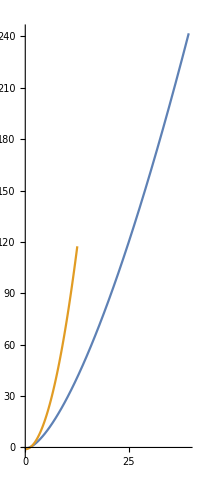

```mathematica
ParametricPlot[{
{t^2,t(t^2-1)},
{2t,-1+3 t^2}
},{t,0,2π}
]
```

```mathematica
D[t(t^2-1),t]
```

-1+3 t^2

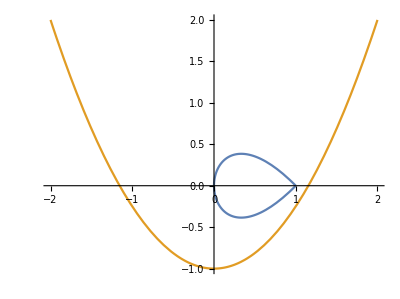

```mathematica
ParametricPlot[{
{t^2,t(t^2-1)},
{2t,-1+3 t^2}
},{t,-1,1}
]
```

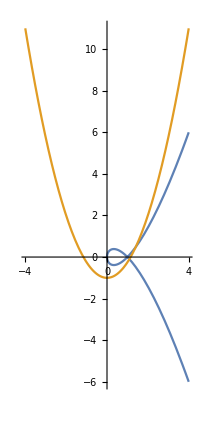

```mathematica
ParametricPlot[{
{t^2,t(t^2-1)},
{2t,-1+3 t^2}
},{t,-2,2}
]
```

```mathematica
∫_a^b √(x'[t]^2+y'[t]^2)ⅆt
```

∫_a^b √(x'[t]^2+y'[t]^2)ⅆt

```mathematica
With[{a=0,b=1,x=Function[t,t^2],y=Function[t,t(t^2-1)]},
∫_a^b √(x'[t]^2+y'[t]^2)ⅆt
]
```

∫_0^1 √(4 t^2+(-1+3 t^2)^2)ⅆt

```mathematica
NIntegrate[√(4 t^2+(-1+3 t^2)^2),{t,0,1}]
```

1.3578

```mathematica
Simplify[∫_0^1 √(4 t^2+(-1+3 t^2)^2)ⅆt]
```

∫_0^1 √(1-2 t^2+9 t^4)ⅆt

```mathematica
With[{a=0,b=1,x=Function[t,t^2],y=Function[t,t(t^2-1)]},
Manipulate[
NIntegrate[√(x'[t]^2+y'[t]^2)ⅆt,{t,a,b}]
,{{a,0},-1,1},{{b,1},-1,1}]
]
```

Manipulate::vsform: Manipulate argument {{0,0},-1,1} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {{1,1},-1,1} does not have the correct form for a variable specification.

Manipulate[NIntegrate[√((Function[t,t^2]'[t])^2+(Function[t,t (t^2-1)]'[t])^2) ⅆt,{t,0,1}],{{0,0},-1,1},{{1,1},-1,1}]

```mathematica
With[{a=0,b=1,x=Function[t,t^2],y=Function[t,t(t^2-1)]},
Manipulate[
NIntegrate[√(x'[t]^2+y'[t]^2)ⅆt,{t,a,b}]
,{{a,0},-1,1},{{b,1},-1,1}]
]
```

Manipulate::vsform: Manipulate argument {{0,0},-1,1} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {{1,1},-1,1} does not have the correct form for a variable specification.

Manipulate[NIntegrate[√((Function[t,t^2]'[t])^2+(Function[t,t (t^2-1)]'[t])^2) ⅆt,{t,0,1}],{{0,0},-1,1},{{1,1},-1,1}]

```mathematica
With[{a=0,b=1,x=Function[t,t^2],y=Function[t,t(t^2-1)]},
Manipulate[
NIntegrate[√(x'[t]^2+y'[t]^2)ⅆt,{t,a,b}]
,{a,0,1},{b,1,2}]
]
```

Manipulate::vsform: Manipulate argument {0,0,1} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {1,1,2} does not have the correct form for a variable specification.

Manipulate[NIntegrate[√((Function[t,t^2]'[t])^2+(Function[t,t (t^2-1)]'[t])^2) ⅆt,{t,0,1}],{0,0,1},{1,1,2}]

```mathematica
With[{x=Function[t,t^2],y=Function[t,t(t^2-1)]},
Manipulate[
NIntegrate[√(x'[t]^2+y'[t]^2)ⅆt,{t,a,b}]
,{{a,0},-1,1},{{b,1},-1,1}]
]
```

NIntegrate::inumr: The integrand √(4 t^2+(-1+3 t^2)^2) ⅆt has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.026,1}}.

NIntegrate::inumr: The integrand √(4 t^2+(-1+3 t^2)^2) ⅆt has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.18,1}}.

```mathematica
Normalize@{a,f[a]}.
Normalize@{1,f'[b]}
```

a/(√(Abs[a]^2+Abs[f[a]]^2) √(1+Abs[f'[b]]^2))+(f[a] f'[b])/(√(Abs[a]^2+Abs[f[a]]^2) √(1+Abs[f'[b]]^2))

```mathematica
FullSimplify[
Normalize@{a,f[a]}.
Normalize@{1,f'[b]}
,{a,b,f[a],f'[b]}∈Reals]
```

(a+f[a] f'[b])/(√((a^2+f[a]^2) (1+f'[b]^2)))

```mathematica
FullSimplify[
Integrate[Normalize@{a,f[a]}.
Normalize@{1,f'[b]},{x,a,b}]
,{a,b,f[a],f'[b]}∈Reals]
```

-((a-b) (a+f[a] f'[b]))/(√((a^2+f[a]^2) (1+f'[b]^2)))

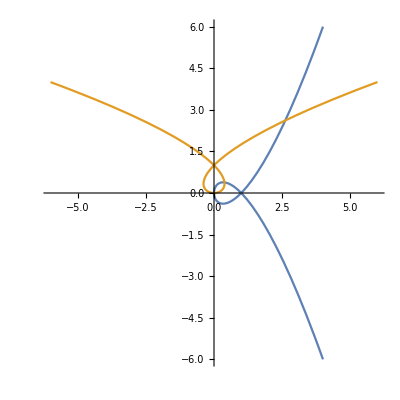

```mathematica
ParametricPlot[{
{t^2,t(t^2-1)},
{t(t^2-1),t^2}
},{t,-2,2}
]
```

```mathematica
f[{x[t],y[t]}]=={y[t],x[t]}
```

f[{x[t],y[t]}]=={y[t],x[t]}

```mathematica
Reduce[f[{x[t],y[t]}]=={y[t],x[t]}]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[f[{x[t],y[t]}]=={y[t],x[t]}]

```mathematica
f[{1,0}]=={0,1}
```

f[{1,0}]=={0,1}

```mathematica
{a,b}.RotationMatrix[θ]
```

{a Cos[θ]+b Sin[θ],b Cos[θ]-a Sin[θ]}

```mathematica
{a,b}.RotationMatrix[π/2]
```

{b,-a}

```mathematica
{b,a}=={a,b}.RotationMatrix[π/2].{1,-1}
```

{b,a}==a+b

```mathematica
IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
{b,a}=={a,b}.RotationMatrix[π/2].{1,-1}
```

```mathematica
{{1,0},{0,-1}}
```

{{1,0},{0,-1}}

```mathematica
{b,a}=={a,b}.RotationMatrix[π/2].{{1,0},{0,-1}}
```

True

```mathematica
TraditionalForm[{b,a}=={a,b}.RotationMatrix[π/2].{{1,0},{0,-1}}]
```

True

```mathematica
TraditionalForm[{a,b}.RotationMatrix[π/2].{{1,0},{0,-1}}]
```

{b,a}

```mathematica
TraditionalForm[{{a,b},RotationMatrix[π/2],{{1,0},{0,-1}}}]
```

(a | b
{0,-1} | {1,0}
{1,0} | {0,-1})

```mathematica
Map[TraditionalForm,{{a,b},RotationMatrix[π/2],{{1,0},{0,-1}}}]
```

{{a,b},(0 | -1
1 | 0),(1 | 0
0 | -1)}

```mathematica
RotationMatrix[π/2].{{1,0},{0,-1}}
```

{{0,1},{1,0}}

```mathematica
Transpose[IdentityMatrix[2]]
```

{{1,0},{0,1}}

```mathematica
A.IdentityMatrix[2]==λ IdentityMatrix[2]
```

A.{{1,0},{0,1}}=={{λ,0},{0,λ}}

```mathematica
A.IdentityMatrix[2]==IdentityMatrix[2]
```

A.{{1,0},{0,1}}=={{1,0},{0,1}}

```mathematica
A.IdentityMatrix[2]=={{0,1},{1,0}}
```

A.{{1,0},{0,1}}=={{0,1},{1,0}}

```mathematica
Solve[A.IdentityMatrix[2]=={{0,1},{1,0}},A]
```

{}

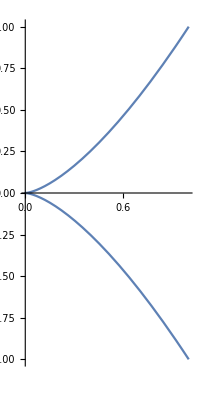

```mathematica
ParametricPlot[
{t^2,t^3}
,{t,-1,1}]
```

```mathematica
Solve[x[t]==t^2∧y[t]==t^3,y[t]]
```

{}

```mathematica
√x[t]==t
```

```mathematica
y[x[t]]==(√x[t])^3
```

y[x[t]]==x[t]^(3/2)

```mathematica
y[x]==(√x)^3
```

y[x]==x^(3/2)

```mathematica
f[x]==f[x-α]+α
```

f[x]==α+f[x-α]

```mathematica
f[0]==0∧f[x]==f[x-α]+α
```

f[0]==0&&f[x]==α+f[x-α]

```mathematica
Reduce[f[0]==0&&f[x]==α+f[x-α]]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[f[0]==0&&f[x]==α+f[x-α]]

```mathematica
(1-a)p+a q/.{p->{x[t],y[t]},q->{b,c}}
```

{a b+(1-a) x[t],a c+(1-a) y[t]}

```mathematica
ParametricPlot3D[
{Cos[θ], Sin[θ],θ}
,{θ,0,2π}
]
```

```mathematica
(1-a)p+a q/.{p->{Cos[θ], Sin[θ],θ},q->{0,2π,0}}
```

{(1-a) Cos[θ],2 a π+(1-a) Sin[θ],(1-a) θ}

```mathematica
Manipulate[
ParametricPlot3D[{
{Cos[θ], Sin[θ],θ},
{0,2π,0},
{(1-a) Cos[θ],2 a π+(1-a) Sin[θ],(1-a) θ}
},{θ,0,2π}
]
,{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot3D[{
{Cos[θ], Sin[θ],θ},
{t,0,0},
{(1-a) Cos[θ],2 a π+(1-a) Sin[θ],(1-a) θ}
},{θ,0,2π}
]
,{a,0,1}]
```

```mathematica
(1-a)p+a q/.{p->{Cos[θ], Sin[θ],θ},q->{t,0,0}}
```

{a t+(1-a) Cos[θ],(1-a) Sin[θ],(1-a) θ}

```mathematica
Manipulate[
ParametricPlot3D[{
{Cos[θ], Sin[θ],θ},
{t,0,0},
{a t+(1-a) Cos[θ],(1-a) Sin[θ],(1-a) θ}
},{θ,0,2π}
]
,{a,0,1}]
```

```mathematica
(1-a)p+a q/.{p->{Cos[θ], Sin[θ],θ},q->{θ,0,0}}
```

{a θ+(1-a) Cos[θ],(1-a) Sin[θ],(1-a) θ}

```mathematica
Manipulate[
ParametricPlot3D[{
{Cos[θ], Sin[θ],θ},
{θ,0,0},
{a θ+(1-a) Cos[θ],(1-a) Sin[θ],(1-a) θ}
},{θ,0,2π}
]
,{a,0,1}]
```

```mathematica
(1-a)p+a q/.{p->{Cos[θ],Sin[θ]},q->{θ,0}}
```

{a θ+(1-a) Cos[θ],(1-a) Sin[θ]}

```mathematica
Manipulate[
ParametricPlot[{
{Cos[θ], Sin[θ]},
{θ,0},
{a θ+(1-a) Cos[θ],(1-a) Sin[θ]}
},{θ,0,2π}
]
,{a,0,1}]
```



```mathematica
ParametricPlot[{
{Cos[θ], Sin[θ]}
},{θ,0,2π}
]
```

```mathematica
Manipulate[
ParametricPlot[{
{Cos[θ], Sin[θ]},
{θ,0},
{a θ+(1-a) Cos[θ],(1-a) Sin[θ]}
},{θ,0,2π},
PlotRange->{{-1,2π},{-1,1}}]
,{a,0,1}]
```

```mathematica
∫_-1^1 √(1+f'[t]^2)ⅆt
```

∫_-1^1 √(1+f'[t]^2)ⅆt

```mathematica
(1-a)f[x]+a g[x]
```

(1-a) f[x]+a g[x]

```mathematica
(1-a) x+a x^2
```

(1-a) x+a x^2

```mathematica
Simplify[(1-a) x+a x^2]
```

x+a (-1+x) x

```mathematica
Expand[x+a (-1+x) x]
```

x-a x+a x^2

```mathematica
√(1+D[(x-a x+a x^2),a]^2)
```

√(1+(-x+x^2)^2)

```mathematica
D[√(1+(-x+x^2)^2),f[a]]-D[D[√(1+(-x+x^2)^2),f'[a]],a]==0
```

True

```mathematica
D[√(1+(-x+x^2)^2),f[a]]-D[D[√(1+(-x+x^2)^2),f'[a]],a]
```

0

```mathematica
D[√(1+(-x+x^2)^2),f[x]]-D[D[√(1+(-x+x^2)^2),f'[x]],x]==0
```

True

```mathematica
FullSimplify[
Normalize[{x,x}].
Normalize[{x,x^2}]
,x∈Reals]
```

(1+x)/(√2 √(1+x^2))

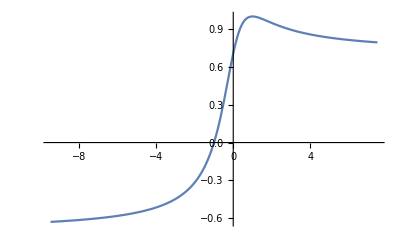

```mathematica
Plot[(1+x)/(√2 √(1+x^2)),{x,-9.493333333333336,7.493333333333335}]
```

```mathematica
(1-(1+x)/(√2 √(1+x^2)))x+((1+x)/(√2 √(1+x^2)))f[x]
```

x (1-(1+x)/(√2 √(1+x^2)))+((1+x) f[x])/(√2 √(1+x^2))

```mathematica
FullSimplify[
Normalize[{x,x}].
Normalize[{x,f[x]}]==(1+x)/(√2 √(1+x^2))
,x∈Reals]
```

1+x==√((1+x^2)/(x^2+Abs[f[x]]^2)) (x+f[x]) Sign[x]

```mathematica
FullSimplify[
Normalize[{x,x}].
Normalize[{x,f[x]}]==(1+x)/(√2 √(1+x^2))
,{f[x],x}∈Reals]
```

(-(1+x)/(√(1+x^2))+((x+f[x]) Sign[x])/(√(x^2+f[x]^2)))/(√2)==0

```mathematica
Reduce[(-(1+x)/(√(1+x^2))+((x+f[x]) Sign[x])/(√(x^2+f[x]^2)))/(√2)==0]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(-(1+x)/(√(1+x^2))+((x+f[x]) Sign[x])/(√(x^2+f[x]^2)))/(√2)==0]

```mathematica
FullSimplify[
Solve[Normalize[{x,x}].
Normalize[{x,f[x]}]==(1+x)/(√2 √(1+x^2)),f[x]]
,{f[x],x}∈Reals]
```

$Aborted

Power::infy: Infinite expression 1/0. encountered.

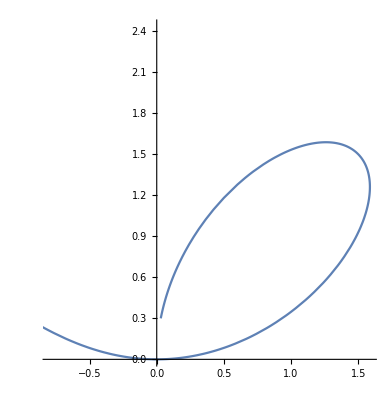

```mathematica
ParametricPlot[
{(3t)/(1+t^3),(3 t^2)/(1+t^3)}
,{t,-1,10}]
```

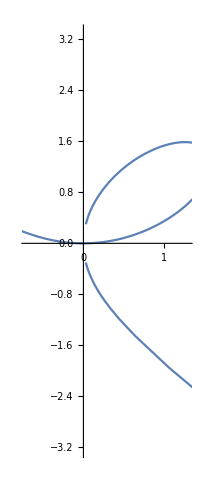

```mathematica
ParametricPlot[
{(3t)/(1+t^3),(3 t^2)/(1+t^3)}
,{t,-10,10}]
```

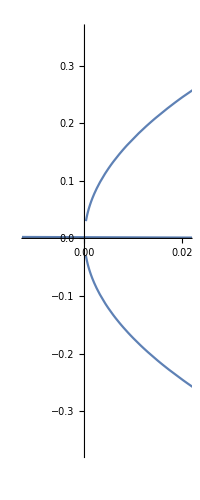

```mathematica
ParametricPlot[
{(3t)/(1+t^3),(3 t^2)/(1+t^3)}
,{t,-100,100}]
```

```mathematica
ParametricPlot[
{(3t)/(1+t^3),(3 t^2)/(1+t^3)}
,{t,-10,10}]
```

-Graphics-

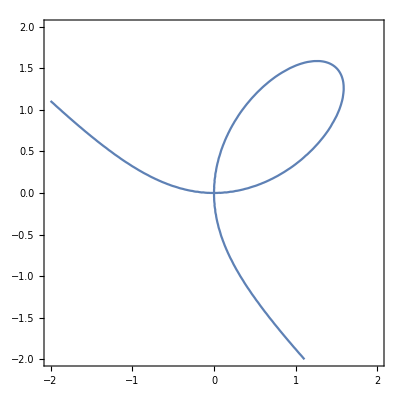

```mathematica
ContourPlot[3x y==x^3+y^3,{x,-2,2},{y,-2,2}]
```

```mathematica
f[α]==f[x-α]+f[α]
```

f[α]==f[x-α]+f[α]

```mathematica
f[x]==f[x-α]+f[α]
```

f[x]==f[x-α]+f[α]

```mathematica
f[x]==f[x-α]+f[α]∧f[β]==γ
```

f[x]==f[x-α]+f[α]&&f[β]==γ

```mathematica
Identity[x]==0.RotationMatrix[θ]
```

x=={{0.,0.},{0.,0.}}

```mathematica
Norm[{x,x}]
```

√2 Abs[x]

```mathematica
Integrate[Norm[{x,x}],{x,0,1}]
```

1/(√2)

```mathematica
Integrate[Abs[Norm[{x,x}]],{x,0,1}]
```

1/(√2)

```mathematica
Integrate[D[Norm[{x,x}],x],{x,0,1}]
```

√2

```mathematica
f:x->x^2
```

f:x→x^2

```mathematica
f:x/.f:x->x^2
```

f:x^2

```mathematica
Γ
```

Γ

```mathematica
Γ:x
```

Γ:x

```mathematica
Abs[α'[t]]==√(x'[t]^2+y'[t]^2)
```

Abs[α'[t]]==√(x'[t]^2+y'[t]^2)

```mathematica
DSolve[Abs[α'[t]]==√(x'[t]^2+y'[t]^2),{x[t],y[t],α[t]},{t}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[Abs[α'[t]]==√(x'[t]^2+y'[t]^2),{x[t],y[t],α[t]},{t}]



```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
f:x^2->x
```

f:x^2→x

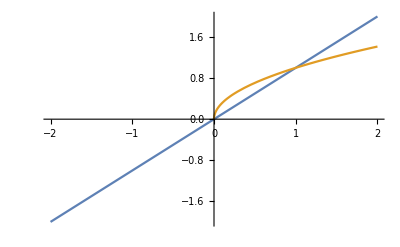

```mathematica
Plot[{x,√x},{x,-2,2}]
```

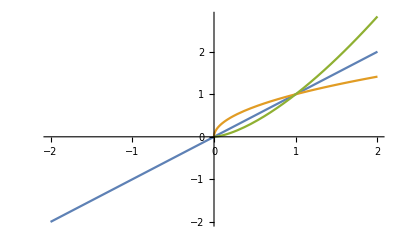

```mathematica
Plot[{x,√x,√(x^3)},{x,-2,2}]
```

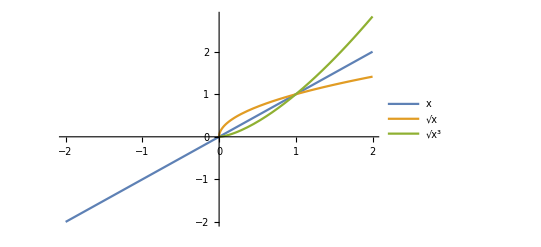

```mathematica
Plot[{x,√x,√(x^3)},{x,-2,2},PlotLegends->"Expressions"]
```

```mathematica
Solve[f[x^2]==x,f,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[f[x^2]==x,f,ℝ]

```mathematica
Solve[f[x^2]==x,f]
```

{}

```mathematica
Reduce[f[x^2]==x,f]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[f[x^2]==x,f]

```mathematica
InverseFunction[f][x^2]
```

f^(-1)[x^2]

```mathematica
{f[x^2],x}
```

{f[x^2],x}

```mathematica
Map[InverseFunction[f],Out[132]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

{x^2,f^(-1)[x]}

```mathematica
D[x,x]
```

1

```mathematica
20 8
```

160

```mathematica
x^2+4x+2
```

2+4 x+x^2

```mathematica
FullSimplify[2+4 x+x^2]
```

2+x (4+x)

```mathematica
x^2+2x+1
```

1+2 x+x^2

```mathematica
Factor[1+2 x+x^2]
```

(1+x)^2

```mathematica
y[x]==x^2+2x+1
```

y[x]==1+2 x+x^2

```mathematica
Reduce[y[x]==1+2 x+x^2]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[y[x]==1+2 x+x^2]

```mathematica
FullForm@((1+x)^2)
```

Power[Plus[1,x],2]

```mathematica
Power[Plus[1,x],2]
RightComposition[Function[x,x^2],Function[x,x+1]]
```

(1+x)^2

Function[x,x^2]/*Function[x,x+1]

```mathematica
RightComposition[Function[x,x^2],Function[x,x+1]][x]
```

1+x^2

```mathematica
Composition[Function[x,x^2],Function[x,x+1]][x]
```

(1+x)^2

```mathematica
InverseFunction[Composition[Function[x,x^2],Function[x,x+1]]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Function[x,-1+x]@*Function[x,-√x]

```mathematica
InverseFunction[Composition[Function[x,x^2],Function[x,x+1]]][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-1-√x

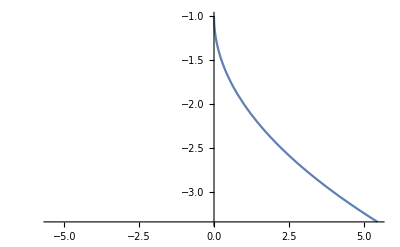

```mathematica
Plot[-1-√x,{x,-5.46,5.46}]
```

```mathematica
Plot[-1-√x,{x,-5.46,5.46}][x^2]
```

(-Graphics-)[x^2]

```mathematica
InverseFunction[Composition[Function[x,x^2],Function[x,x+1]]][x^2]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-1-√(x^2)

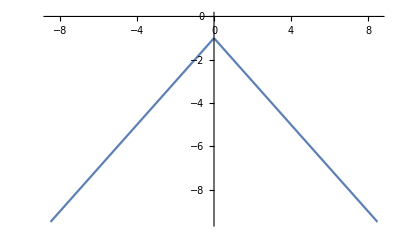

```mathematica
Plot[-1-√(x^2),{x,-8.493333333333334,8.493333333333334}]
```